## Derive a smooth waveshaping function :

{{a→-1/2,b→0,c→3/2,d→0}}

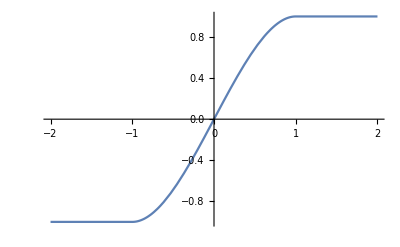

```mathematica
y[x_]:=a x^3 + b x^2 + c x + d;
soln1 =Solve[{y[1] == 1,y'[1]==0,y[-1]==-1,y'[-1]==0},{a,b,c,d}]
f[x_]:= If[x>1,1,If[x<-1,-1,x(3-x^2)/2]]
Plot[f[x]/.soln1,{x,-2,2}]
```

## Implement the anti-aliased waveshaper

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -100 Cos[(1609 π)/8192].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -100 Cos[(203 π)/1024].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -100 Cos[(1639 π)/8192].

General::stop: Further output of N::meprec will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{0.,32769.},{-5.50120543734147×10^2070,3.32231806299675×10^2070}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

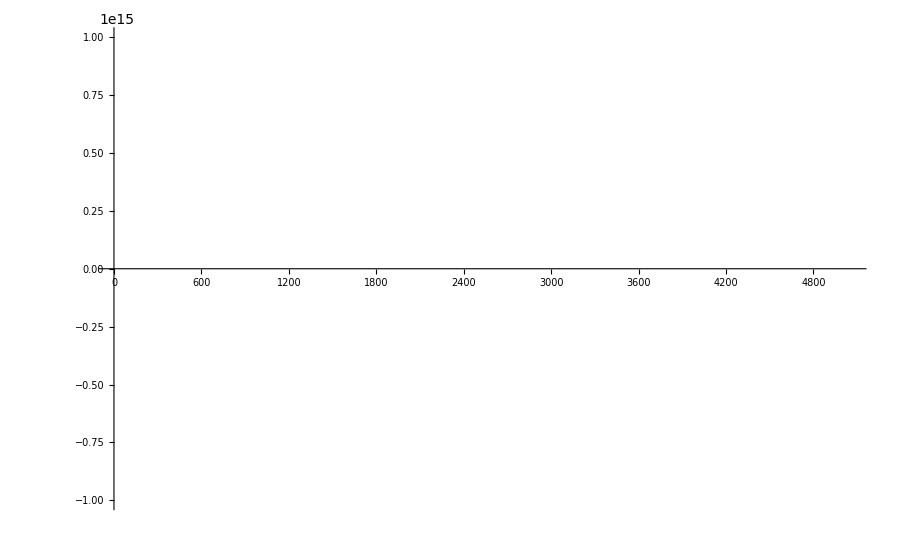

```mathematica
AAWaveshaper[X_,fc_,Q_,sr_,f_]:=Module[{i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,output,waveShapedOutput,error},
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;

(* update the first state variable to correct the output value in the direction of the error between the actual output and the waveshaped output *)
waveShapedOutput = f[v2];
error = v2 - waveShapedOutput;
ic1 -= error/a2;
];

output
]

length = 2^15;
input = Table[100Sin[2 π 30 x],{x,0,1,1/length}];
output = AAWaveshaper[input,2000,0.5,48000,f];
ListLinePlot[output]
```